## Seasonal Ricker model - EWS in rnb - Intervals

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-2;
bh=-0.0568;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_rnb_tmax200";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

2

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

```mathematica
stateVals
```

{Breeding,Non-breeding,Total}

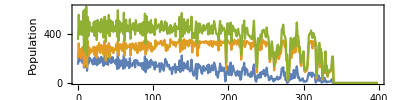

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},All}]
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;3]],{"Breeding","Non-breeding","Total"},Spacings->{0,0.2},LabelStyle->10]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.5];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

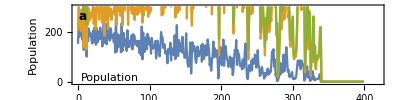

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,300}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (Mean +/- SD)

### Variance

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Variance"][[1,1]];
```

```mathematica
dfEwsMeans[[1]]
```

{Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {1308.8,1304.76,1297.27,1291.81,1278.56,1277.89,1285.84,1285.14,1256.51,1243.29,1224.08,1204.16,«28»,1110.67,1107.66,1106.67,1110.26,1122.01,1126.77,1125.,1128.91,1130.37,1139.75,«126»}+{«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-24.4803,-24.5179,-25.5529,-14.0487,-1.56822,-5.28405,«39»,-45.8372,-40.7273,-36.1686,-33.3803,-47.0844,«62»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{1308.8,1304.76,1297.27,1291.81,1278.56,1277.89,«39»,1126.77,1125.,1128.91,1130.37,1139.75,«126»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{24.4803,24.5179,25.5529,14.0487,1.56822,5.28405,«39»,45.8372,40.7273,36.1686,33.3803,47.0844,«62»}+{«19»,«49»,«126»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {1573.61,1554.78,1534.52,1524.83,1480.03,1481.89,1450.39,1436.93,1434.27,1381.03,1359.86,1311.47,«28»,1121.92,1117.25,1108.5,1085.4,1083.1,1088.84,1082.59,1079.91,1080.09,1078.04,«127»}+{-«19»,«50»} cannot be combined.

Thread::tdlen: Objects of unequal length in {1573.61,1554.78,1534.52,1524.83,1480.03,1481.89,1450.39,1436.93,1434.27,1381.03,1359.86,1311.47,«28»,1121.92,1117.25,1108.5,1085.4,1083.1,1088.84,1082.59,1079.91,1080.09,1078.04,«127»}+{«19»,«49»,«63»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-132.775,-130.694,-134.257,-128.895,-67.9137,-100.026,«39»,-38.7566,-47.7556,-51.5896,-38.5369,-53.006,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{132.775,130.694,134.257,128.895,67.9137,100.026,«39»,38.7566,47.7556,51.5896,38.5369,53.006,«63»}+{«19»,«49»,«127»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {4436.15,4377.23,4348.35,4309.45,4162.37,4162.57,4101.81,4085.91,4030.31,3901.56,3820.72,3685.79,«27»,3012.67,3018.46,2998.74,2972.99,2953.99,2960.5,2976.54,2955.9,2957.36,2955.88,2958.39,«127»}+«1» cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-270.648,-262.328,-309.37,-263.151,-68.8752,-98.7989,«39»,-22.6798,-10.7991,-22.9727,-13.6305,-21.1884,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{270.648,262.328,309.37,263.151,68.8752,98.7989,24.0636,«38»,22.6798,10.7991,22.9727,13.6305,21.1884,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

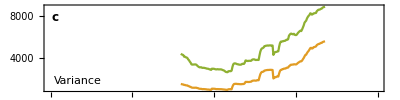

```mathematica
(* Plot EWS *)
plotVar=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Skewness"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.206723,0.197186,0.19193,0.169384,0.219024,0.236587,0.247185,0.248855,0.228418,0.231513,0.239868,«29»,0.176647,0.174044,0.183034,0.17684,0.194684,0.186369,0.177324,0.17372,0.172235,0.167898,«126»}+{-«19»,«50»} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.206723,0.197186,0.19193,0.169384,0.219024,0.236587,0.247185,0.248855,0.228418,0.231513,0.239868,«29»,0.176647,0.174044,0.183034,0.17684,0.194684,0.186369,0.177324,0.17372,0.172235,0.167898,«126»}+{«19»,«49»,«62»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.308457,-0.292769,-0.317917,-0.318917,-0.255365,-0.245674,«40»,-0.0416617,-0.0520421,-0.036883,-0.0495433,«62»}+{«20»,«49»,«126»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.206723,0.197186,0.19193,0.169384,0.219024,0.236587,«39»,0.186369,0.177324,0.17372,0.172235,0.167898,«126»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.308457,0.292769,0.317917,0.318917,0.255365,0.245674,«39»,0.0493817,0.0416617,0.0520421,0.036883,0.0495433,«62»}+{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {-0.793291,-0.820421,-0.828329,-0.83993,-0.805079,-0.831212,-0.828035,-0.841897,-0.844419,-0.801887,-0.824159,«29»,-1.5641,-1.5821,-1.60092,-1.65415,-1.65843,-1.63182,-1.63793,-1.64961,-1.66432,-1.67457,«127»}+{«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.0301916,-0.0313387,-0.0358683,-0.058206,-0.101198,-0.107294,«39»,-0.848125,-0.841706,-0.825268,-0.856445,-0.826094,«63»}+«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.0301916,0.0313387,0.0358683,0.058206,0.101198,0.107294,«39»,0.848125,0.841706,0.825268,0.856445,0.826094,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {-0.388604,-0.402838,-0.402249,-0.428762,-0.371261,-0.37793,-0.361999,-0.358906,-0.373336,-0.323624,-0.345254,«29»,-0.499514,-0.51425,-0.520756,-0.542449,-0.538498,-0.536547,-0.553697,-0.561931,-0.573344,-0.588713,«127»}+«1» cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.162062,-0.152353,-0.158633,-0.160848,-0.0837816,-0.0778716,«40»,-0.0265595,-0.0113956,-0.0236128,-0.0120844,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.162062,0.152353,0.158633,0.160848,0.0837816,0.0778716,«39»,0.0369315,0.0265595,0.0113956,0.0236128,0.0120844,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

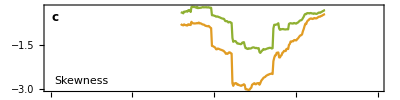

```mathematica
(* Plot EWS *)
plotSkew=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.230223,0.23023,0.230201,0.230381,0.229249,0.230465,0.231704,0.232457,0.231323,0.230411,0.230162,«29»,0.246638,0.247186,0.248394,0.249634,0.251769,0.253163,0.253927,0.255233,0.256443,0.258109,«126»}+{-«22»,«49»,«62»} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.230223,0.23023,0.230201,0.230381,0.229249,0.230465,0.231704,0.232457,0.231323,0.230411,0.230162,«29»,0.246638,0.247186,0.248394,0.249634,0.251769,0.253163,0.253927,0.255233,0.256443,0.258109,«126»}+{«22»,«49»,«62»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.00318026,-0.00377692,-0.00334508,-0.00279794,-0.000532854,«41»,-0.00978941,-0.00934079,-0.00950958,-0.0103833,«62»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.230223,0.23023,0.230201,0.230381,0.229249,0.230465,«39»,0.253163,0.253927,0.255233,0.256443,0.258109,«126»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.00318026,0.00377692,0.00334508,0.00279794,0.000532854,0.000284887,«40»,0.00978941,0.00934079,0.00950958,0.0103833,«62»}+{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.133553,0.132395,0.13155,0.130953,0.128765,0.128782,0.12714,0.126444,0.126172,0.123398,0.122409,«29»,0.107238,0.106831,0.106375,0.105039,0.104839,0.105094,0.104742,0.104491,0.104357,0.10408,«127»}+{«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.133553,0.132395,0.13155,0.130953,0.128765,0.128782,0.12714,0.126444,0.126172,0.123398,0.122409,«29»,0.107238,0.106831,0.106375,0.105039,0.104839,0.105094,0.104742,0.104491,0.104357,0.10408,«127»}+{«22»,«50»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.005347,-0.00528402,-0.00537839,-0.0053789,-0.00259194,«41»,-0.00226665,-0.00250899,-0.00187883,-0.00260071,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.005347,0.00528402,0.00537839,0.0053789,0.00259194,0.00443051,«40»,0.00226665,0.00250899,0.00187883,0.00260071,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.146664,0.145511,0.145174,0.144545,0.141886,0.142123,0.140986,0.140798,0.140027,0.137539,0.136376,«29»,0.122778,0.122362,0.122003,0.121552,0.12173,0.122169,0.121842,0.121895,0.121889,0.121884,«127»}+{«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.00449239,-0.00450861,-0.00512535,-0.00463165,-0.000994276,«41»,-0.000551559,-0.000256871,-0.00050507,-0.000228986,«63»}+{«20»,«49»,«127»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.00449239,0.00450861,0.00512535,0.00463165,0.000994276,0.00190658,«40»,0.000551559,0.000256871,0.00050507,0.000228986,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

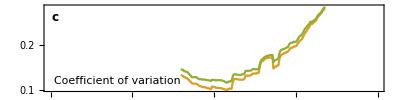

```mathematica
(* Plot EWS *)
plotCv=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Smax"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {133.302,103.931,104.747,100.815,89.9154,88.8429,70.6834,71.9419,84.6109,67.8575,88.3218,69.0632,80.8474,101.657,117.969,130.676,159.185,162.777}+{-13.1003,-1.74491,«8»,-4.56542,-3.40869} cannot be combined.

Thread::tdlen: Objects of unequal length in {133.302,103.931,104.747,100.815,89.9154,88.8429,70.6834,71.9419,84.6109,67.8575,88.3218,69.0632,80.8474,101.657,117.969,130.676,159.185,162.777}+{13.1003,1.74491,3.21787,«7»,4.56542,3.40869} cannot be combined.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{-13.1003,-1.74491,-3.21787,-6.00076,-11.6244,-7.80271,-5.66257,-2.97477,-13.5694,-3.20374,-4.56542,-3.40869}+{133.302,103.931,104.747,«12»,130.676,159.185,162.777}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{13.1003,1.74491,3.21787,6.00076,11.6244,7.80271,5.66257,2.97477,13.5694,3.20374,4.56542,3.40869}+{133.302,103.931,104.747,100.815,«11»,130.676,159.185,162.777}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,169.,179.,189.,199.,209.,219.,229.,239.,249.,259.,269.,279.,289.,299.,309.,319.,329.},{-13.1003,-1.74491,-3.21787,-6.00076,-11.6244,-7.80271,-5.66257,-2.97477,-13.5694,-3.20374,-4.56542,-3.40869}+{133.302,«16»,162.777}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {183.045,150.991,130.32,139.177,100.372,80.9532,65.8077,74.6507,172.493,146.959,220.038,257.894,257.218,393.996,537.372,659.169,909.435,1079.89}+{-36.3471,-37.5852,-42.8435,«7»,-80.0385,-93.5116} cannot be combined.

Thread::tdlen: Objects of unequal length in {183.045,150.991,130.32,139.177,100.372,80.9532,65.8077,74.6507,172.493,146.959,220.038,257.894,257.218,393.996,537.372,659.169,909.435,1079.89}+{36.3471,37.5852,42.8435,«7»,80.0385,93.5116} cannot be combined.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{-36.3471,-37.5852,-42.8435,-54.818,-2.82069,-12.3775,-15.3087,-3.05902,-145.767,-79.9493,-80.0385,-93.5116}+{183.045,150.991,130.32,«12»,659.169,909.435,1079.89}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{36.3471,37.5852,42.8435,54.818,2.82069,12.3775,15.3087,3.05902,145.767,79.9493,80.0385,93.5116}+{183.045,150.991,130.32,139.177,«11»,659.169,909.435,1079.89}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,169.,179.,189.,199.,209.,219.,229.,239.,249.,259.,269.,279.,289.,299.,309.,319.,329.},{-36.3471,-37.5852,-42.8435,-54.818,-2.82069,-12.3775,-15.3087,-3.05902,-145.767,-79.9493,-80.0385,-93.5116}+{183.045,«16»,1079.89}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {593.461,443.994,429.427,453.098,321.217,259.373,187.502,185.097,328.705,284.225,429.523,487.89,539.772,812.493,1074.32,1303.26,1730.41,1984.86}+{-2.94485,-62.0336,«8»,-153.166,-150.827} cannot be combined.

Thread::tdlen: Objects of unequal length in {593.461,443.994,429.427,453.098,321.217,259.373,187.502,185.097,328.705,284.225,429.523,487.89,539.772,812.493,1074.32,1303.26,1730.41,1984.86}+{2.94485,62.0336,55.3956,«7»,153.166,150.827} cannot be combined.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{-2.94485,-62.0336,-55.3956,-70.5536,-72.133,-21.3897,-25.7952,-2.84207,-223.503,-85.5597,-153.166,-150.827}+{593.461,443.994,429.427,«12»,1303.26,1730.41,1984.86}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{2.94485,62.0336,55.3956,70.5536,72.133,21.3897,25.7952,2.84207,223.503,85.5597,153.166,150.827}+{593.461,443.994,429.427,453.098,«11»,1303.26,1730.41,1984.86}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,169.,179.,189.,199.,209.,219.,229.,239.,249.,259.,269.,279.,289.,299.,309.,319.,329.},{-2.94485,-62.0336,-55.3956,-70.5536,-72.133,-21.3897,-25.7952,-2.84207,-223.503,-85.5597,-153.166,-150.827}+{593.461,«16»,1984.86}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

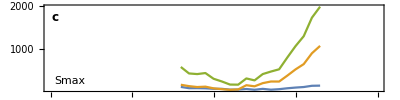

```mathematica
(* Plot variance EWS for display param *)
plotSmax=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.101962,0.0851694,0.092477,0.0899496,0.0812,0.0784472,0.0644159,0.0656434,0.0747535,0.0602055,0.07805,0.0608371,0.0688372,0.0857977,0.101023,0.110786,0.145567,0.151163}+{-0.0119165,-0.00745877,«9»,-0.000715966} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.101962,0.0851694,0.092477,0.0899496,0.0812,0.0784472,0.0644159,0.0656434,0.0747535,0.0602055,0.07805,0.0608371,0.0688372,0.0857977,0.101023,0.110786,0.145567,0.151163}+{0.0119165,0.00745877,«9»,0.000715966} cannot be combined.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{-0.0119165,-0.00745877,-0.00973313,-0.0105086,-0.0134213,-0.00436292,-0.00262442,-0.00586992,-0.0121916,-0.00428712,-0.00786012,-0.000715966}+{0.101962,0.0851694,«14»,0.145567,0.151163}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{0.0119165,0.00745877,0.00973313,0.0105086,0.0134213,0.00436292,0.00262442,0.00586992,0.0121916,0.00428712,0.00786012,0.000715966}+{0.101962,0.0851694,0.092477,«13»,0.145567,0.151163}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,169.,179.,189.,199.,209.,219.,229.,239.,249.,259.,269.,279.,289.,299.,309.,319.,329.},{-0.0119165,-0.00745877,-0.00973313,-0.0105086,-0.0134213,-0.00436292,-0.00262442,-0.00586992,-0.0121916,-0.00428712,-0.00786012,-0.000715966}+{«20»,«16»,«19»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.11576,0.110198,0.108244,0.127095,0.0894724,0.0751243,0.0609124,0.0503747,0.0925218,0.0747149,0.0841115,0.0898018,0.0999095,0.126605,0.156921,0.163498,0.184511,0.199285}+{-0.0133306,-0.0164037,«9»,-0.00642766} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.11576,0.110198,0.108244,0.127095,0.0894724,0.0751243,0.0609124,0.0503747,0.0925218,0.0747149,0.0841115,0.0898018,0.0999095,0.126605,0.156921,0.163498,0.184511,0.199285}+{0.0133306,0.0164037,«9»,0.00642766} cannot be combined.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{-0.0133306,-0.0164037,-0.0131677,-0.032076,-0.000455308,-0.00709348,-0.00385651,-0.0160897,-0.0686476,-0.027814,-0.0134371,-0.00642766}+{0.11576,0.110198,«14»,0.184511,0.199285}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{0.0133306,0.0164037,0.0131677,0.032076,0.000455308,0.00709348,0.00385651,0.0160897,0.0686476,0.027814,0.0134371,0.00642766}+{0.11576,0.110198,0.108244,«13»,0.184511,0.199285}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,169.,179.,189.,199.,209.,219.,229.,239.,249.,259.,269.,279.,289.,299.,309.,319.,329.},{-0.0133306,-0.0164037,-0.0131677,-0.032076,-0.000455308,-0.00709348,-0.00385651,-0.0160897,-0.0686476,-0.027814,-0.0134371,-0.00642766}+{«20»,«16»,«20»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {0.134007,0.115943,0.130454,0.147195,0.106458,0.0883567,0.0668731,0.0555652,0.0846414,0.0721244,0.0867023,0.0931523,0.10566,0.140986,0.172968,0.182921,0.212431,0.229659}+{-0.00751191,-0.00594792,«9»,-0.000575495} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.134007,0.115943,0.130454,0.147195,0.106458,0.0883567,0.0668731,0.0555652,0.0846414,0.0721244,0.0867023,0.0931523,0.10566,0.140986,0.172968,0.182921,0.212431,0.229659}+{0.00751191,0.00594792,«9»,0.000575495} cannot be combined.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{-0.00751191,-0.00594792,-0.00860658,-0.00756851,-0.0242571,-0.00549684,-0.00465927,-0.0142839,-0.0520259,-0.0127168,-0.00175,-0.000575495}+{0.134007,0.115943,«14»,0.212431,0.229659}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,169,179,189,199,209,219,229,239,249,259,269,279,289,299,309,319,329},{0.00751191,0.00594792,0.00860658,0.00756851,0.0242571,0.00549684,0.00465927,0.0142839,0.0520259,0.0127168,0.00175,0.000575495}+{0.134007,0.115943,0.130454,«13»,0.212431,0.229659}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,169.,179.,189.,199.,209.,219.,229.,239.,249.,259.,269.,279.,289.,299.,309.,319.,329.},{-0.00751191,-0.00594792,-0.00860658,-0.00756851,-0.0242571,-0.00549684,-0.00465927,-0.0142839,-0.0520259,-0.0127168,-0.00175,-0.000575495}+{«20»,«16»,«19»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

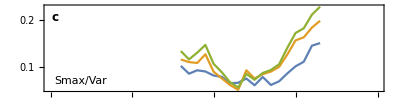

```mathematica
(* Plot EWS *)
plotSmaxVar=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {-0.416757,-0.422585,-0.417674,-0.399262,-0.376355,-0.37674,-0.377234,-0.374879,-0.362037,-0.353936,«31»,-0.210386,-0.210619,-0.20454,-0.204998,-0.21003,-0.206111,-0.200744,-0.196228,-0.19405,«126»}+{-0.0156962,«49»,«62»} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.416757,-0.422585,-0.417674,-0.399262,-0.376355,-0.37674,-0.377234,-0.374879,-0.362037,-0.353936,«31»,-0.210386,-0.210619,-0.20454,-0.204998,-0.21003,-0.206111,-0.200744,-0.196228,-0.19405,«126»}+{0.0156962,«49»,«62»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.0156962,-0.00151405,-0.00162405,-0.0228301,-0.0516596,-0.0544968,«40»,-0.0200785,-0.0213902,-0.0267899,-0.0230837,«62»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.416757,-0.422585,-0.417674,-0.399262,-0.376355,-0.37674,«39»,-0.21003,-0.206111,-0.200744,-0.196228,-0.19405,«126»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.0156962,0.00151405,0.00162405,0.0228301,0.0516596,«41»,0.0200785,0.0213902,0.0267899,0.0230837,«62»}+{-0.416757,«49»,«126»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {-0.486516,-0.475663,-0.48022,-0.477584,-0.469022,-0.451723,-0.441296,-0.442802,-0.440972,-0.428643,-0.4147,«30»,-0.260481,-0.248987,-0.251213,-0.249547,-0.252725,-0.249805,-0.248827,-0.248205,-0.242834,«127»}+{-«22»,«49»,«63»} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.486516,-0.475663,-0.48022,-0.477584,-0.469022,-0.451723,-0.441296,-0.442802,-0.440972,-0.428643,-0.4147,«30»,-0.260481,-0.248987,-0.251213,-0.249547,-0.252725,-0.249805,-0.248827,-0.248205,-0.242834,«127»}+{«22»,«49»,«63»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.00151212,-0.00527185,-0.0187585,-0.0143967,-0.00414012,-0.0159505,«40»,-0.0227943,-0.0230502,-0.0198504,-0.0118821,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.00151212,0.00527185,0.0187585,0.0143967,0.00414012,0.0159505,«40»,0.0227943,0.0230502,0.0198504,0.0118821,«63»}+{-«19»,«49»,«127»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

Thread::tdlen: Objects of unequal length in {-0.618545,-0.618004,-0.621253,-0.612822,-0.601386,-0.596764,-0.597323,-0.599994,-0.591465,-0.581398,-0.57029,«29»,-0.389954,-0.385253,-0.377843,-0.373902,-0.372687,-0.380527,-0.378384,-0.373192,-0.370298,-0.361785,«127»}+{«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{-0.0567513,-0.0509059,-0.0436087,-0.0539984,-0.0630736,-0.0677734,«40»,-0.0371594,-0.0397293,-0.0404932,-0.031152,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,«127»},{0.0567513,0.0509059,0.0436087,0.0539984,0.0630736,0.0677734,«39»,0.0421564,0.0371594,0.0397293,0.0404932,0.031152,«63»}+{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,«127»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

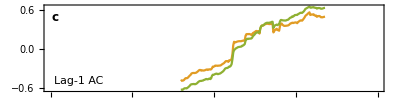

```mathematica
(* Plot EWS *)
plotAc1=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.965126 | -0.96873 | -0.915838 | -0.985237 | -0.96873 | -0.97431 | -0.989305 | -0.983493 | -0.991863 | -0.988027 | -0.980587 | -0.976518 | -0.987794 | -0.967103 | -0.980006 | -0.975007 | -0.983726 | -0.969427 | -0.986283 | -0.980238 | -0.978262 | -0.986516 | -0.979425 | -0.983144 | -0.983261 | -0.988375 | -0.987329 | -0.989073 | -0.986516 | -0.963499 | -0.992677 | -0.984423 | -0.983493 | -0.983726 | -0.979657 | -0.966754 | -0.989305 | -0.989538 | -0.965475 | -0.988724 | -0.989422 | -0.973961 | -0.987562 | -0.984888 | -0.971752 | -0.979657 | -0.975937 | -0.993258 | -0.983958 | -0.985818 | -0.929904 | -0.982563 | -0.986399 | -0.988143 | -0.986167 | -0.970939 | -0.980006 | -0.972566 | -0.981749 | -0.988259 | -0.980587 | -0.981285 | -0.96687 | -0.965475 | -0.986981 | -0.989073 | -0.982912 | -0.98082 | -0.987097 | -0.993839 | -0.99163 | -0.981517 | -0.976053 | -0.988143 | -0.990119 | -0.984888 | -0.983842 | -0.982563 | -0.987097 | -0.991282 | -0.983726 | -0.992095 | -0.984772 | -0.980471 | -0.98791 | -0.97059 | -0.981401 | -0.987678 | -0.975472 | -0.988027 | -0.969195 | -0.981633 | -0.987213 | -0.97059 | -0.987562 | -0.987794 | -0.975588 | -0.989189 | -0.988957 | -0.984772
Non-breeding | -0.919791 | -0.951642 | -0.87213 | -0.972334 | -0.968033 | -0.981517 | -0.982214 | -0.981517 | -0.975588 | -0.980587 | -0.925138 | -0.957338 | -0.972799 | -0.936879 | -0.975472 | -0.955362 | -0.977681 | -0.956408 | -0.978727 | -0.969544 | -0.975588 | -0.984888 | -0.965475 | -0.933508 | -0.970939 | -0.957105 | -0.963383 | -0.920488 | -0.972334 | -0.948852 | -0.978843 | -0.971171 | -0.97524 | -0.951642 | -0.980355 | -0.964545 | -0.974077 | -0.958849 | -0.918977 | -0.952339 | -0.962337 | -0.941761 | -0.975821 | -0.969079 | -0.934205 | -0.952223 | -0.971404 | -0.983144 | -0.965824 | -0.979657 | -0.916536 | -0.971287 | -0.968498 | -0.982331 | -0.950015 | -0.972217 | -0.936181 | -0.957687 | -0.94397 | -0.983377 | -0.970009 | -0.918396 | -0.946178 | -0.952572 | -0.980355 | -0.979076 | -0.983144 | -0.962337 | -0.9771 | -0.98884 | -0.985818 | -0.971171 | -0.971404 | -0.962685 | -0.981982 | -0.96501 | -0.980936 | -0.976518 | -0.984539 | -0.97152 | -0.956873 | -0.979425 | -0.929555 | -0.969195 | -0.972915 | -0.896658 | -0.979192 | -0.98082 | -0.973961 | -0.975356 | -0.973496 | -0.958384 | -0.96129 | -0.964313 | -0.976402 | -0.959779 | -0.949201 | -0.968614 | -0.976867 | -0.966754
Total | -0.953386 | -0.954432 | -0.861319 | -0.975821 | -0.959547 | -0.981866 | -0.981633 | -0.981517 | -0.983144 | -0.976983 | -0.963034 | -0.967684 | -0.971287 | -0.924673 | -0.968033 | -0.937576 | -0.979541 | -0.952572 | -0.97896 | -0.979192 | -0.97152 | -0.984772 | -0.958733 | -0.958035 | -0.960477 | -0.975124 | -0.979657 | -0.952688 | -0.980355 | -0.936181 | -0.987329 | -0.978262 | -0.975124 | -0.971171 | -0.974659 | -0.960012 | -0.980471 | -0.979308 | -0.892241 | -0.968846 | -0.979192 | -0.946178 | -0.984888 | -0.973612 | -0.938739 | -0.97059 | -0.965126 | -0.987678 | -0.974426 | -0.983028 | -0.867132 | -0.973612 | -0.967219 | -0.986864 | -0.972217 | -0.965243 | -0.934321 | -0.940831 | -0.939436 | -0.986981 | -0.974775 | -0.937228 | -0.944667 | -0.952456 | -0.982796 | -0.983144 | -0.9771 | -0.970706 | -0.971752 | -0.986399 | -0.990352 | -0.975821 | -0.967451 | -0.975007 | -0.984307 | -0.980006 | -0.977216 | -0.970822 | -0.988143 | -0.984539 | -0.959198 | -0.985586 | -0.97152 | -0.971985 | -0.976518 | -0.919558 | -0.973961 | -0.986283 | -0.971985 | -0.984888 | -0.95048 | -0.972101 | -0.979541 | -0.958849 | -0.977448 | -0.975124 | -0.946876 | -0.980471 | -0.985353 | -0.975937

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.125836 | 0.166638 | 0.683813 | 0.154432 | 0.457367 | -0.376344 | 0.436675 | 0.613136 | 0.469573 | 0.462831 | 0.188259 | 0.232549 | -0.178843 | 0.145248 | -0.0564371 | 0.114211 | 0.302877 | 0.186283 | 0.599535 | 0.597675 | 0.574542 | -0.0383028 | 0.332752 | 0.595001 | 0.43621 | 0.660913 | 0.495495 | 0.628829 | 0.520837 | 0.253008 | 0.372508 | -0.39041 | 0.508515 | -0.361232 | -0.252543 | 0.226039 | 0.636501 | 0.632084 | 0.185004 | -0.323685 | 0.273583 | 0.644987 | 0.0651555 | 0.485382 | 0.628015 | 0.308457 | 0.843766 | 0.395292 | -0.2322 | 0.512351 | 0.592328 | 0.555246 | 0.150015 | -0.243708 | -0.28916 | -0.16873 | -0.50061 | 0.875966 | 0.396687 | -0.407498 | 0.900378 | 0.388317 | 0.326591 | 0.581633 | 0.581285 | 0.380413 | 0.715199 | 0.111305 | 0.290323 | 0.540599 | -0.195466 | 0.576402 | 0.334496 | 0.610346 | 0.19163 | 0.322755 | 0.778669 | 0.843766 | 0.216507 | 0.390061 | 0.443069 | -0.287765 | 0.530137 | 0.0108689 | 0.495728 | 0.499913 | -0.00610288 | 0.0887533 | 0.0995641 | -0.171636 | 0.103865 | 0.164661 | 0.53188 | 0.581633 | 0.110607 | 0.260099 | -0.0394653 | -0.277652 | -0.264167 | -0.340424
Non-breeding | 0.111189 | 0.0549259 | 0.831444 | 0.680558 | 0.881662 | 0.695205 | 0.204301 | 0.342633 | 0.458646 | 0.372973 | -0.489567 | -0.627085 | -0.518861 | 0.385876 | 0.725429 | -0.225341 | 0.54862 | -0.548852 | 0.647428 | 0.646382 | 0.48515 | 0.321709 | -0.13653 | 0.797036 | -0.275094 | 0.100145 | 0.377623 | 0.541412 | 0.44737 | -0.279279 | 0.524789 | -0.385179 | 0.753211 | -0.238128 | 0.50526 | 0.475734 | 0.444348 | 0.808079 | -0.455623 | 0.745539 | -0.257425 | 0.784133 | 0.305667 | 0.546876 | 0.790759 | 0.470851 | 0.583028 | 0.105144 | 0.224876 | -0.0557396 | 0.874455 | 0.82447 | -0.454345 | 0.04737 | 0.208486 | 0.20465 | 0.661842 | 0.863412 | -0.378785 | -0.242546 | 0.821447 | 0.793316 | 0.197443 | 0.802964 | 0.3288 | 0.643708 | 0.728916 | 0.525022 | -0.00203429 | -0.108166 | 0.0481837 | 0.643592 | -0.243941 | 0.719849 | 0.0737576 | 0.608137 | 0.265911 | 0.718686 | 0.145365 | 0.262191 | 0.592677 | 0.6873 | 0.547341 | 0.0610869 | 0.656611 | 0.217669 | 0.265795 | 0.0917756 | 0.0453938 | -0.0154025 | -0.297646 | 0.194769 | 0.15757 | 0.858762 | 0.242197 | -0.0709677 | -0.196396 | -0.39227 | -0.429468 | 0.702296
Total | 0.217902 | -0.00842778 | 0.87213 | 0.267655 | 0.839117 | 0.268468 | 0.28265 | 0.510724 | 0.484801 | 0.491311 | -0.48143 | -0.280674 | -0.457367 | -0.165591 | 0.360418 | 0.0111014 | 0.401569 | -0.422261 | 0.623598 | 0.675211 | 0.325545 | 0.0846847 | -0.0353967 | 0.701133 | -0.0215635 | 0.414705 | 0.294391 | 0.47864 | 0.480732 | 0.0302819 | 0.0921244 | -0.660796 | 0.66347 | -0.453763 | 0.0852659 | 0.474804 | 0.678582 | 0.663702 | -0.0419064 | 0.386574 | 0.118977 | 0.581866 | 0.0194711 | 0.532229 | 0.659285 | 0.256844 | 0.815519 | -0.115606 | -0.210578 | 0.379483 | 0.771811 | 0.761697 | -0.340773 | -0.0885208 | -0.275676 | 0.0349317 | 0.0650392 | 0.893868 | 0.580238 | -0.497007 | 0.900727 | 0.52723 | 0.376693 | 0.811799 | 0.48608 | 0.613252 | 0.718105 | 0.275559 | 0.14862 | 0.161407 | 0.0150538 | 0.683348 | 0.19256 | 0.669515 | 0.259866 | 0.38297 | 0.705667 | 0.810171 | 0.364603 | 0.175356 | 0.402964 | 0.19163 | 0.582331 | -0.0625981 | 0.7517 | 0.445045 | 0.0600407 | 0.0746876 | 0.234641 | -0.123976 | -0.133275 | 0.195466 | 0.358559 | 0.724731 | 0.183842 | 0.186167 | -0.129904 | -0.248707 | -0.441441 | 0.0708515

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.928277 | 0.6093 | 0.682185 | 0.89782 | 0.860389 | 0.741819 | 0.889683 | 0.50154 | 0.710549 | 0.477826 | 0.833537 | 0.884801 | 0.814705 | 0.923743 | 0.872246 | 0.778204 | 0.879686 | 0.966638 | 0.762976 | 0.456553 | 0.956176 | 0.843185 | 0.889102 | 0.909096 | 0.855275 | 0.915606 | 0.831212 | 0.882709 | 0.827492 | 0.940366 | 0.642778 | 0.758094 | 0.558035 | 0.773787 | 0.904795 | 0.942807 | 0.788434 | 0.771462 | 0.942575 | 0.558965 | 0.69753 | 0.586864 | 0.862714 | 0.892357 | 0.818541 | 0.85202 | 0.909212 | 0.475385 | 0.693112 | 0.665795 | 0.86934 | 0.835397 | 0.809009 | 0.830049 | 0.88236 | 0.916652 | 0.95943 | 0.93002 | 0.949201 | 0.713223 | 0.857483 | 0.923394 | 0.655333 | 0.861552 | 0.499564 | 0.728451 | 0.870387 | 0.842023 | 0.830049 | 0.473874 | 0.803894 | 0.841906 | 0.931415 | 0.86469 | 0.725661 | 0.800756 | 0.720546 | 0.920023 | 0.84551 | 0.855158 | 0.739611 | 0.611043 | 0.791223 | 0.714967 | 0.541994 | 0.56408 | 0.694275 | 0.727754 | 0.906306 | 0.710201 | 0.893868 | 0.771462 | 0.921302 | 0.721128 | 0.893287 | 0.888986 | 0.833885 | 0.679628 | 0.747864 | 0.764138
Non-breeding | 0.954781 | 0.945597 | 0.982331 | 0.953153 | 0.950712 | 0.91642 | 0.961755 | 0.838303 | 0.94397 | 0.689858 | 0.963964 | 0.908399 | 0.957687 | 0.959663 | 0.946992 | 0.929439 | 0.924557 | 0.95943 | 0.882825 | 0.820517 | 0.976867 | 0.936879 | 0.959895 | 0.98082 | 0.925952 | 0.967568 | 0.923859 | 0.950363 | 0.963383 | 0.950131 | 0.925719 | 0.869573 | 0.759489 | 0.978843 | 0.965591 | 0.937111 | 0.925952 | 0.952804 | 0.977448 | 0.702296 | 0.858065 | 0.661842 | 0.952223 | 0.954432 | 0.930718 | 0.952921 | 0.946643 | 0.793316 | 0.834467 | 0.831444 | 0.830631 | 0.94955 | 0.958384 | 0.961174 | 0.984074 | 0.968963 | 0.97152 | 0.950015 | 0.963848 | 0.946295 | 0.942807 | 0.968149 | 0.863993 | 0.966986 | 0.91084 | 0.973961 | 0.948271 | 0.951293 | 0.890497 | 0.73159 | 0.886312 | 0.963964 | 0.968149 | 0.911305 | 0.908864 | 0.854228 | 0.955478 | 0.952223 | 0.885266 | 0.959547 | 0.901075 | 0.949782 | 0.910956 | 0.91084 | 0.842371 | 0.82075 | 0.951293 | 0.939552 | 0.96594 | 0.900262 | 0.858413 | 0.90898 | 0.956059 | 0.778204 | 0.94769 | 0.961872 | 0.939785 | 0.959082 | 0.906306 | 0.940134
Total | 0.954432 | 0.87399 | 0.950944 | 0.930485 | 0.911421 | 0.861319 | 0.958849 | 0.771462 | 0.869573 | 0.593258 | 0.94397 | 0.909212 | 0.936763 | 0.953037 | 0.925603 | 0.916536 | 0.922697 | 0.970474 | 0.845859 | 0.704156 | 0.974077 | 0.908282 | 0.922813 | 0.968846 | 0.900029 | 0.964661 | 0.879221 | 0.946295 | 0.940715 | 0.953734 | 0.865853 | 0.859924 | 0.710549 | 0.92909 | 0.950944 | 0.972334 | 0.906423 | 0.926882 | 0.966638 | 0.648009 | 0.819239 | 0.653008 | 0.94118 | 0.937809 | 0.897472 | 0.896077 | 0.93839 | 0.777274 | 0.725196 | 0.819355 | 0.834118 | 0.900494 | 0.886661 | 0.928044 | 0.956989 | 0.957454 | 0.973031 | 0.966173 | 0.962453 | 0.890729 | 0.916303 | 0.952921 | 0.721244 | 0.919791 | 0.86934 | 0.940947 | 0.920837 | 0.937111 | 0.890148 | 0.611043 | 0.900378 | 0.894798 | 0.959198 | 0.887475 | 0.878756 | 0.80959 | 0.925719 | 0.939087 | 0.903981 | 0.925836 | 0.850741 | 0.924208 | 0.94304 | 0.831677 | 0.678233 | 0.818309 | 0.87678 | 0.900145 | 0.946876 | 0.798082 | 0.893636 | 0.857716 | 0.951293 | 0.737169 | 0.951991 | 0.943854 | 0.910142 | 0.932461 | 0.891078 | 0.916768

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.789474 | -0.824561 | -0.660819 | -0.871345 | -0.824561 | -0.906433 | -0.695906 | -0.894737 | -0.602339 | -0.74269 | -0.74269 | -0.777778 | -0.74269 | -0.80117 | -0.730994 | -0.415205 | -0.637427 | -0.0526316 | -0.918129 | -0.719298 | -0.0994152 | -0.918129 | -0.883041 | -0.403509 | -0.28655 | -0.497076 | -0.74269 | -0.660819 | -0.824561 | -0.754386 | -0.80117 | -0.824561 | -0.74269 | -0.824561 | -0.578947 | -0.777778 | -0.836257 | -0.918129 | -0.672515 | -0.859649 | -0.894737 | -0.54386 | -0.789474 | -0.80117 | -0.450292 | -0.403509 | -0.368421 | -0.824561 | -0.812865 | -0.906433 | -0.602339 | -0.777778 | -0.695906 | -0.906433 | -0.766082 | -0.415205 | -0.461988 | -0.122807 | -0.578947 | -0.789474 | -0.614035 | -0.766082 | -0.28655 | 0.391813 | -0.906433 | -0.894737 | -0.824561 | -0.614035 | -0.508772 | -0.859649 | -0.929825 | -0.766082 | -0.847953 | -0.766082 | -0.859649 | -0.836257 | -0.847953 | -0.777778 | -0.871345 | -0.929825 | -0.719298 | -0.80117 | -0.74269 | -0.637427 | -0.80117 | -0.766082 | -0.789474 | -0.906433 | -0.847953 | -0.789474 | -0.637427 | -0.777778 | -0.859649 | -0.54386 | -0.649123 | -0.789474 | -0.80117 | -0.824561 | -0.836257 | -0.508772
Non-breeding | -0.602339 | -0.54386 | 0.134503 | -0.824561 | -0.578947 | -0.754386 | -0.812865 | -0.836257 | -0.614035 | -0.497076 | -0.590643 | -0.824561 | -0.824561 | -0.567251 | -0.368421 | 0.0760234 | -0.672515 | -0.684211 | -0.54386 | -0.637427 | 0.333333 | -0.789474 | -0.789474 | -0.391813 | 0.157895 | -0.122807 | -0.730994 | 0.216374 | -0.391813 | -0.263158 | -0.789474 | -0.380117 | -0.730994 | -0.438596 | -0.111111 | -0.754386 | -0.894737 | -0.473684 | -0.555556 | -0.438596 | -0.859649 | -0.146199 | -0.415205 | -0.74269 | 0.298246 | -0.649123 | -0.216374 | -0.789474 | -0.54386 | -0.894737 | -0.672515 | -0.80117 | -0.181287 | -0.122807 | -0.590643 | -0.415205 | -0.146199 | 0.251462 | 0.122807 | -0.649123 | -0.578947 | -0.204678 | -0.111111 | 0.695906 | -0.707602 | -0.730994 | -0.707602 | 0.146199 | -0.497076 | -0.80117 | -0.871345 | -0.134503 | -0.111111 | -0.520468 | -0.894737 | -0.883041 | -0.74269 | -0.672515 | -0.836257 | -0.438596 | -0.263158 | -0.415205 | 0.146199 | -0.391813 | -0.614035 | -0.695906 | -0.461988 | -0.80117 | -0.754386 | -0.789474 | -0.614035 | -0.766082 | -0.48538 | -0.28655 | -0.426901 | -0.578947 | -0.719298 | -0.532164 | -0.660819 | -0.0994152
Total | -0.625731 | -0.684211 | -0.146199 | -0.847953 | -0.578947 | -0.836257 | -0.719298 | -0.836257 | -0.532164 | -0.602339 | -0.520468 | -0.754386 | -0.684211 | -0.672515 | -0.54386 | -0.111111 | -0.578947 | -0.00584795 | -0.660819 | -0.719298 | 0.497076 | -0.695906 | -0.777778 | -0.321637 | 0.333333 | -0.22807 | -0.695906 | 0.169591 | -0.54386 | -0.146199 | -0.859649 | -0.602339 | -0.602339 | -0.625731 | -0.0994152 | -0.684211 | -0.824561 | -0.660819 | -0.578947 | -0.777778 | -0.824561 | -0.239766 | -0.578947 | -0.74269 | 0.0409357 | -0.403509 | -0.263158 | -0.777778 | -0.637427 | -0.80117 | -0.614035 | -0.74269 | -0.508772 | -0.637427 | -0.754386 | -0.0292398 | -0.157895 | 0.251462 | -0.169591 | -0.567251 | -0.461988 | -0.578947 | -0.111111 | 0.578947 | -0.754386 | -0.859649 | -0.684211 | -0.122807 | -0.345029 | -0.859649 | -0.883041 | -0.28655 | -0.461988 | -0.660819 | -0.906433 | -0.859649 | -0.74269 | -0.719298 | -0.824561 | -0.871345 | -0.426901 | -0.730994 | -0.28655 | -0.497076 | -0.707602 | -0.730994 | -0.684211 | -0.80117 | -0.824561 | -0.754386 | -0.578947 | -0.80117 | -0.789474 | -0.239766 | -0.497076 | -0.578947 | -0.649123 | -0.637427 | -0.80117 | -0.216374

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

7

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.380117 | 0.649123 | 0.859649 | 0.438596 | 0.333333 | -0.239766 | 0.707602 | 0.719298 | 0.567251 | 0.450292 | 0.719298 | 0.74269 | 0.766082 | 0.520468 | 0.532164 | 0.80117 | 0.80117 | 0.906433 | 0.660819 | 0.0994152 | 0.918129 | 0.777778 | 0.391813 | 0.847953 | 0.894737 | 0.637427 | 0.719298 | 0.777778 | 0.719298 | 0.754386 | 0.48538 | 0.789474 | 0.532164 | 0.625731 | 0.707602 | 0.625731 | 0.695906 | 0.812865 | -0.134503 | 0.251462 | 0.660819 | 0.649123 | 0.80117 | 0.836257 | 0.883041 | 0.812865 | 0.637427 | 0.719298 | 0.649123 | 0.578947 | 0.660819 | 0.836257 | 0.660819 | 0.94152 | 0.0877193 | 0.80117 | 0.836257 | 0.625731 | 0.578947 | 0.625731 | 0.74269 | 0.602339 | 0.508772 | 0.953216 | 0.380117 | 0.894737 | 0.625731 | 0.871345 | 0.54386 | 0.450292 | 0.309942 | 0.707602 | 0.578947 | 0.532164 | 0.672515 | 0.789474 | 0.298246 | 0.356725 | 0.578947 | 0.777778 | 0.754386 | 0.473684 | 0.754386 | 0.625731 | 0.333333 | 0.602339 | 0.0877193 | 0.707602 | 0.567251 | 0.836257 | 0.426901 | 0.695906 | 0.649123 | 0.438596 | 0.777778 | 0.707602 | 0.824561 | 0.695906 | 0.497076 | 0.695906
Non-breeding | 0.520468 | 0.649123 | 0.812865 | 0.660819 | 0.707602 | 0.567251 | 0.719298 | 0.80117 | 0.730994 | 0.426901 | 0.766082 | 0.239766 | 0.707602 | 0.508772 | 0.824561 | 0.859649 | 0.684211 | 0.719298 | 0.625731 | 0.239766 | 0.918129 | 0.380117 | 0.637427 | 0.672515 | 0.894737 | 0.695906 | 0.637427 | 0.789474 | 0.789474 | 0.824561 | 0.251462 | 0.789474 | 0.438596 | 0.74269 | 0.918129 | 0.918129 | 0.707602 | 0.730994 | 0.181287 | 0.602339 | 0.567251 | 0.660819 | 0.777778 | 0.824561 | 0.859649 | 0.871345 | 0.637427 | 0.555556 | 0.578947 | 0.777778 | 0.578947 | 0.602339 | 0.684211 | 0.918129 | 0.48538 | 0.883041 | 0.74269 | 0.766082 | 0.789474 | 0.637427 | 0.707602 | 0.847953 | 0.520468 | 0.953216 | 0.157895 | 0.836257 | 0.508772 | 0.94152 | 0.380117 | 0.567251 | -0.22807 | 0.894737 | 0.707602 | 0.695906 | 0.333333 | 0.730994 | 0.649123 | 0.777778 | 0.602339 | 0.918129 | 0.461988 | 0.672515 | 0.80117 | 0.754386 | 0.649123 | 0.684211 | 0.28655 | 0.602339 | 0.532164 | 0.602339 | 0.730994 | 0.707602 | 0.836257 | 0.497076 | 0.859649 | 0.74269 | 0.614035 | 0.625731 | 0.672515 | 0.766082
Total | 0.426901 | 0.555556 | 0.80117 | 0.520468 | 0.426901 | 0.438596 | 0.719298 | 0.812865 | 0.649123 | 0.403509 | 0.812865 | 0.555556 | 0.812865 | 0.426901 | 0.695906 | 0.836257 | 0.812865 | 0.894737 | 0.707602 | 0.216374 | 0.94152 | 0.730994 | 0.450292 | 0.812865 | 0.859649 | 0.637427 | 0.777778 | 0.80117 | 0.871345 | 0.824561 | 0.625731 | 0.80117 | 0.520468 | 0.590643 | 0.824561 | 0.707602 | 0.766082 | 0.824561 | -0.111111 | 0.473684 | 0.555556 | 0.625731 | 0.766082 | 0.836257 | 0.859649 | 0.859649 | 0.567251 | 0.672515 | 0.660819 | 0.719298 | 0.567251 | 0.707602 | 0.649123 | 0.964912 | 0.0994152 | 0.929825 | 0.777778 | 0.672515 | 0.672515 | 0.649123 | 0.777778 | 0.789474 | 0.497076 | 0.94152 | 0.204678 | 0.883041 | 0.625731 | 0.894737 | 0.426901 | 0.567251 | -0.0175439 | 0.859649 | 0.707602 | 0.590643 | 0.497076 | 0.847953 | 0.345029 | 0.555556 | 0.660819 | 0.812865 | 0.789474 | 0.660819 | 0.824561 | 0.672515 | 0.508772 | 0.695906 | 0.0877193 | 0.74269 | 0.859649 | 0.719298 | 0.649123 | 0.660819 | 0.754386 | 0.555556 | 0.766082 | 0.719298 | 0.824561 | 0.707602 | 0.660819 | 0.74269

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.923511 | 0.91642 | 0.935949 | 0.929439 | 0.917815 | 0.735658 | 0.808544 | 0.926533 | 0.813194 | 0.768207 | 0.834932 | 0.937228 | 0.936646 | 0.94304 | 0.918163 | 0.930718 | 0.903051 | 0.952804 | 0.746237 | 0.68172 | 0.937925 | 0.918977 | 0.902354 | 0.963034 | 0.946411 | 0.907236 | 0.810869 | 0.904679 | 0.887126 | 0.928742 | 0.677303 | 0.810171 | 0.752398 | 0.921883 | 0.921767 | 0.802964 | 0.938622 | 0.728916 | 0.85574 | 0.91828 | 0.477477 | 0.923627 | 0.905376 | 0.931183 | 0.958268 | 0.884103 | 0.955246 | 0.813775 | 0.863993 | 0.585586 | 0.920256 | 0.879105 | 0.925603 | 0.904679 | 0.81796 | 0.953967 | 0.89782 | 0.916536 | 0.934554 | 0.890148 | 0.950712 | 0.762395 | 0.928044 | 0.928858 | 0.796571 | 0.917001 | 0.791572 | 0.941064 | 0.842836 | 0.650915 | 0.775995 | 0.927463 | 0.874106 | 0.818192 | 0.882825 | 0.890729 | 0.87957 | 0.844464 | 0.864342 | 0.922581 | 0.856786 | 0.884917 | 0.904446 | 0.863412 | 0.843301 | 0.902586 | 0.919326 | 0.906539 | 0.881314 | 0.870154 | 0.84365 | 0.823888 | 0.847254 | 0.875618 | 0.812961 | 0.837024 | 0.935368 | 0.891892 | 0.914211 | 0.937111
Non-breeding | 0.91642 | 0.902586 | 0.923743 | 0.922232 | 0.923743 | 0.900959 | 0.899564 | 0.922348 | 0.857367 | 0.628015 | 0.895379 | 0.895263 | 0.785062 | 0.943737 | 0.958965 | 0.937576 | 0.871549 | 0.917815 | 0.780878 | 0.690323 | 0.961407 | 0.866434 | 0.916071 | 0.947922 | 0.960942 | 0.920023 | 0.945481 | 0.930369 | 0.914676 | 0.920488 | 0.883871 | 0.897007 | 0.631619 | 0.895612 | 0.964894 | 0.879919 | 0.88329 | 0.885615 | 0.901424 | 0.834118 | 0.53932 | 0.918861 | 0.918628 | 0.91828 | 0.914443 | 0.896542 | 0.947225 | 0.633014 | 0.96315 | 0.751003 | 0.827143 | 0.827376 | 0.926765 | 0.952339 | 0.935251 | 0.939436 | 0.955478 | 0.867132 | 0.945365 | 0.911305 | 0.930718 | 0.897588 | 0.874571 | 0.945713 | 0.907817 | 0.938971 | 0.811334 | 0.949782 | 0.841558 | 0.750421 | 0.304388 | 0.911305 | 0.893171 | 0.852136 | 0.875036 | 0.896309 | 0.956873 | 0.844813 | 0.754025 | 0.960825 | 0.812496 | 0.945365 | 0.954432 | 0.951991 | 0.918396 | 0.88887 | 0.927347 | 0.867713 | 0.909445 | 0.94025 | 0.880965 | 0.891427 | 0.905493 | 0.696019 | 0.812845 | 0.892473 | 0.926649 | 0.897123 | 0.955013 | 0.948503
Total | 0.953618 | 0.925371 | 0.920721 | 0.945946 | 0.927928 | 0.905376 | 0.864342 | 0.952572 | 0.834699 | 0.71764 | 0.868062 | 0.938971 | 0.921767 | 0.949433 | 0.967916 | 0.939669 | 0.916071 | 0.9449 | 0.810753 | 0.737751 | 0.96129 | 0.932578 | 0.920721 | 0.968963 | 0.965708 | 0.933624 | 0.903865 | 0.937228 | 0.923627 | 0.942342 | 0.81982 | 0.880151 | 0.813543 | 0.900145 | 0.962685 | 0.861203 | 0.944667 | 0.880035 | 0.910026 | 0.961755 | 0.5127 | 0.923859 | 0.919907 | 0.951758 | 0.952107 | 0.903633 | 0.938739 | 0.833653 | 0.956059 | 0.769486 | 0.932229 | 0.87492 | 0.936181 | 0.941529 | 0.932113 | 0.954199 | 0.929323 | 0.88143 | 0.941877 | 0.898402 | 0.96036 | 0.869689 | 0.939204 | 0.952107 | 0.802616 | 0.950596 | 0.901889 | 0.959082 | 0.87306 | 0.815054 | 0.676954 | 0.932113 | 0.905376 | 0.872711 | 0.881779 | 0.947341 | 0.909096 | 0.885266 | 0.828887 | 0.947922 | 0.90061 | 0.956292 | 0.951758 | 0.926649 | 0.914908 | 0.921302 | 0.92723 | 0.90898 | 0.923162 | 0.939901 | 0.849927 | 0.913746 | 0.897704 | 0.914211 | 0.845045 | 0.915257 | 0.936298 | 0.912816 | 0.956176 | 0.954548

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;8]]
```

{159.,239.,319.}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,"Total",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

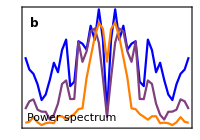

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

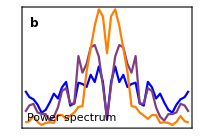

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

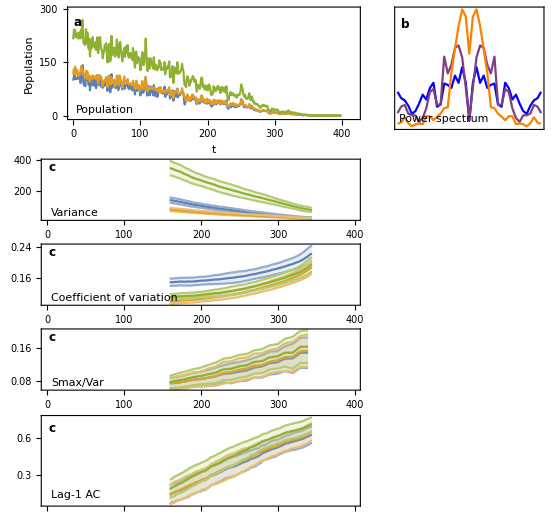

```mathematica
plotGrid
```

```mathematica
Export["figures/intervals_"<>simName<>".png",plotGrid,ImageResolution->200];
```